Climate Model - Muryshev coupled to social dynamics

## Setup

```mathematica
SetDirectory["/Users/tbury/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

## Parameters

### Muryshev parameters

```mathematica
cap=10^9; (* heat capacity *)
rx=5.3*(60*60*24*365); (* radiative perturbing forcing *)
lambda=0.8*(60*60*24*365); (* coeff of climate sensitivity (0.8-2.5 *)
f0=2.5*^-2; (* ocean flux constant (2.5-4.5 *10^-2) *)
```

### Social parameters

```mathematica
κ=0.01;
δ=2;
β=1;
(* response function to temp *)
resType=1; (* 1 linear, 2 logistic, 3 cubic *)
fmax=6;
tempMax=5;
(* linear *)
b1=fmax/tempMax;
c1=0;
(* logistic *)
b2=2fmax;
c2=1;
d2=1;
(* cubic *)
b3=(tempMax^3/fmax)^(1/3);
c3=0;
```

### Conversion factors

```mathematica
ka=1.773*^20; (* moles in atmosphere *)
gtcToMol=8.3259*^13;(* factor from gtC to moles *)
gtcToPpm=gtcToMol*10^6/ka; (* factor from gtc to ppmv *)
```

### Initial conditions (pre-industrial)

```mathematica
cat0=596; (* initial carbon in the atmostphere *)
coc0=1.5*^5; (* initial carbon in the ocean *)
cve0=550; (* initial carbon in veg *)
cso0=1500; (*initical carbon in soil *)
temp0=288.15; (* inital temp *)
```

### Lenton parameters

```mathematica
kp=0.184; (* photosyn rate *)
kr=0.092; (*plant respiration rate *)
kt=0.092; (* turnover rate *)
ksr=0.0337; (* soil respiration rate *)
kc=29*^-6; (* compensation point *)
kM=120*^-6; (* half-saturation point - set to 145 for ocean warming *)
```

```mathematica
ea=54.83; (* plant respiration activation energy *)
kMM=1.478; (* photosyn normalising constnat - set to 1.578 for ocean warming *)
kA=8.7039*^9; (* plant respiration normalising constant &*)
kB=157.072; (* soil respiration normalising constant*)
solar=1368; (* solar flux *)
albedo=0.225; (* surface albedo *)
tauch4=0.0231; (* methane opacity *)
p0=1.4*^11; (* water vapour saturation constant *)
hum=0.6177; (* relative humidity *)
rgas=8.314; (* universal gas constant *)
rho=1027; (* density of sea water *)
lheat=43655; (* latent heat per mole of water *)
σ=5.67*^-8; (* Stefan-Boltzman constant*)
gtcToMol=8.3259*^13; (* factor to go from gtc to moles *)
```

### Simulation

```mathematica
(* vector of noise amplitudes *)
σ={0,0,0,0,0,0.005};
(* initial conditions *)
x0=0.1;
yInit={0,0,0,0,0,x0};
(* time *)
tmax=1200;
dt=1;
tVals=Range[0,tmax,dt];
(* seed number *)
seed=1;
```

### Graphing

```mathematica
(* time ticks *)
timeTicks=Table[{100(i-1),1800+100(i-1)},{i,1,13}];
```

## Functional Forms

### Ocean

```mathematica
(* characteristic c02 solubility in seawater *)
Clear[chi]
chi[temp_]:=0.8;
```

```mathematica
(* buffer factor *)
Clear[zeta]
zeta[temp_,cat_]:=20;
```

```mathematica
(* carbon flux to ocean from atmosphere *)
Clear[foc]
foc[temp_,cat_,coc_]:=f0*chi[temp]*(cat-zeta[temp,cat]*cat0*coc/coc0)
```

### Land

```mathematica
(* atmospheric mixing ratio of co2 in atmosphere *)
Clear[pco2a]
pco2a[cat_]:=(cat+cat0)*gtcToMol/ka
```

```mathematica
(* photosynthesis - from Lenton *)
Clear[photo]
photo[cat_,temp_]:=If[pco2a[cat]>kc&& -15<temp<25,
kp*cve0*kMM*((pco2a[cat]-kc)/(kM+pco2a[cat]-kc))*(((15+temp)^2)*(25-temp)/5625),
0];
```

```mathematica
(* respiration of plants *)
Clear[respp]
respp[temp_,cve_]:=kr*(cve+cve0)*Exp[-(ea/(rgas*(temp+temp0)))]
```

```mathematica
(* turnover of plants *)
Clear[turnover]
turnover[cve_]:=kt*(cve+cve0)
```

```mathematica
(* respiration of soil *)
Clear[resps]
resps[temp_,cso_]:=ksr*(cso+cso0)*kB*Exp[-(308.56/(temp+temp0-227.13))]
```

```mathematica
(* carbon flux to land from atmosphere *)
Clear[fla]
fla[cat_,cve_,cso_,temp_]:=photo[cat,temp]-respp[temp,cve]-resps[temp,cso];
```

### Anthropogenic emissions

```mathematica
(20.3-10.6)/(300-215)
```

0.114118

```mathematica
(* historical emissions from Lenton *)
emissionData={{0,0.35},{50,0.4},{147,2},{180,6.7},{190,7.4},{200,8.5},{210,10.0}};
futureEmissionData={{215,10.6},{220,11.4},{225,12.2},{250,14.5},{275,16.3},{300,20.3},{400,0},{1200,0}} ;(* used by Lenton *)
```

```mathematica
futureEmissionData2={{1200,10.6+((20.3-10.6)/(300-215))*(1200-215)}}; (* linearly increasing energy needs for population growth *)
```

```mathematica
emissions=Interpolation[Union[emissionData,futureEmissionData],InterpolationOrder->1];
emissions2=Interpolation[Union[emissionData,futureEmissionData2],InterpolationOrder->1];
```

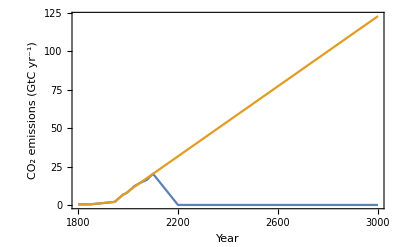

```mathematica
emissionPlot=Plot[{emissions[t],emissions2[t]},{t,0,1200},
PlotRange->All,
FrameTicks->{{Automatic,None},{timeTicks[[1;;;;2]],None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"CO_2 emissions (GtC yr^-1)",None},{"Year",None}}]
```

### Social - cost of global warming

```mathematica
(* social response to temperature function *)
Clear[resLin,resLog,resCub,res]
resLin[temp_]:=b1 temp + c1;
resLog[temp_]:=b2/(1+c2 Exp[-d2 temp])-fmax;
resCub[temp_]:=(temp/b3)^3+c3;
Which[resType==1,res[temp_]:=resLin[temp],
resType==2,res[temp_]:=resLog[temp],
resType==3,res[temp_]:=resCub[temp]]
```

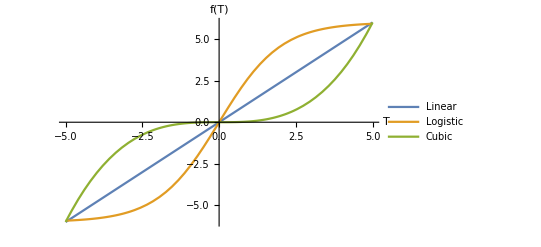

```mathematica
(* Make plot of three functions *)
warmCostPlot=Plot[{resLin[temp],resLog[temp],resCub[temp]},{temp,-tempMax,tempMax},
LabelStyle->14,
AxesLabel->{"T","f(T)"},
PlotLegends->{"Linear","Logistic","Cubic"}]
```

## Stochastic Simulation

### Derivative functions

```mathematica
Clear[f1,f2,f3,f4,f5,f6];
f1[{t_,cat_,coc_,cve_,cso_,temp_,soc_}]:=emissions2[t]*(1-soc)/(1-x0)-foc[temp,cat,coc]-fla[cat,cve,cso,temp];
f2[{t_,cat_,coc_,cve_,cso_,temp_,soc_}]:=foc[temp,cat,coc];
f3[{t_,cat_,coc_,cve_,cso_,temp_,soc_}]:=photo[cat,temp]-respp[temp,cve]-turnover[cve];
f4[{t_,cat_,coc_,cve_,cso_,temp_,soc_}]:=turnover[cve]-resps[temp,cso];
f5[{t_,cat_,coc_,cve_,cso_,temp_,soc_}]:=(1/cap)*(rx*Log[1+cat/cat0]-lambda*temp);
f6[{t_,cat_,coc_,cve_,cso_,temp_,soc_}]:=Which[0≤t≤210,0,
t>210,κ*soc*(1-soc)*(-β+res[temp]+δ*(2soc-1))];
```

```mathematica
f4[{1,1,1,1,1,1,1}]
```

-4.18885

```mathematica
(* data array (cat,coc,cveg,cso,temp,soc) *)
y=ConstantArray[0,{6,tmax+1}];
```

### Implement Euler Muruyama

```mathematica
(* initial conditions *)
y[[;;,1]]=yInit;
```

```mathematica
(* matrix of normal random variables with mean zero, variance Subscript[σ, i] *)
noise=Table[If[σ[[i]]==0,ConstantArray[0,tmax],RandomVariate[NormalDistribution[0,σ[[i]]],tmax]],{i,1,6}];
noise//Dimensions
```

{6,1200}

```mathematica
(* make first 210 timesteps noise-free for social (only introduce social behaviour after 2010) *)
noise[[6,1;;210]]=ConstantArray[0,210];
```

```mathematica
(* set up counter *)
For[i=1,i≤tmax,i++,
(* atmospheric carbon *)
y[[1,i+1]]=y[[1,i]]+f1[Flatten[{i,y[[;;,i]]}]]+noise[[1,i]];
(* oceanic carbon *)
y[[2,i+1]]=y[[2,i]]+f2[Flatten[{i,y[[;;,i]]}]]+noise[[2,i]];
(* veg carbon *)
y[[3,i+1]]=y[[3,i]]+f3[Flatten[{i,y[[;;,i]]}]]+noise[[3,i]];
(* soil carbon *)
y[[4,i+1]]=y[[4,i]]+f4[Flatten[{i,y[[;;,i]]}]]+noise[[4,i]];
(* temp *)
y[[5,i+1]]=y[[5,i]]+f5[Flatten[{i,y[[;;,i]]}]]+noise[[5,i]];
(* social *)
y[[6,i+1]]=y[[6,i]]+f6[Flatten[{i,y[[;;,i]]}]]+noise[[6,i]];
(* make sure proportion of mitigators stay between [0,1] *)
If[y[[6,i+1]]≤0,y[[6,i+1]]=0];
If[y[[6,i+1]]≥1,y[[6,i+1]]=1];
]
```

```mathematica
y//Dimensions
```

{6,1201}

## Plots

### Plots of state variables

```mathematica
(* emissions emissions[t]*(1-x) *)
emissionSeries=Table[emissions2[i-1]*(1-y[[6,i]]),{i,1,tmax+1}];
emissionPlot=ListLinePlot[Transpose[{tVals,emissionSeries}],
PlotRange->{{0,1200},All},
FrameTicks->{{Automatic,None},{timeTicks[[1;;;;2]],None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"CO_2emissions (gtC yr^-1)",None},{"Year",None}}];
```

```mathematica
(* social *)
socPlot=ListLinePlot[Transpose[{tVals[[210;;]],y[[6,210;;]]}],
PlotRange->{{0,1200},All},
FrameTicks->{{Automatic,None},{timeTicks[[1;;;;2]],None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"Proportion mitigators",None},{"Year",None}}];
```

```mathematica
(* carbon in atmosphere in ppmv *)
catPlot=ListLinePlot[Transpose[{tVals,y[[1]]}],
PlotRange->{{0,1200},All},
FrameTicks->{{Automatic,None},{timeTicks[[1;;;;2]],None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"Atmospheric CO_2 (ppmv)",None},{"Year",None}}];
```

```mathematica
(* temperature change *)
tempPlot=ListLinePlot[Transpose[{tVals,y[[5]]}],
PlotRange->{{0,1200},All},
FrameTicks->{{Automatic,None},{timeTicks[[1;;;;2]],None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"Temperature change (K)",None},{"Year",None}}];
```

### Plot Grid

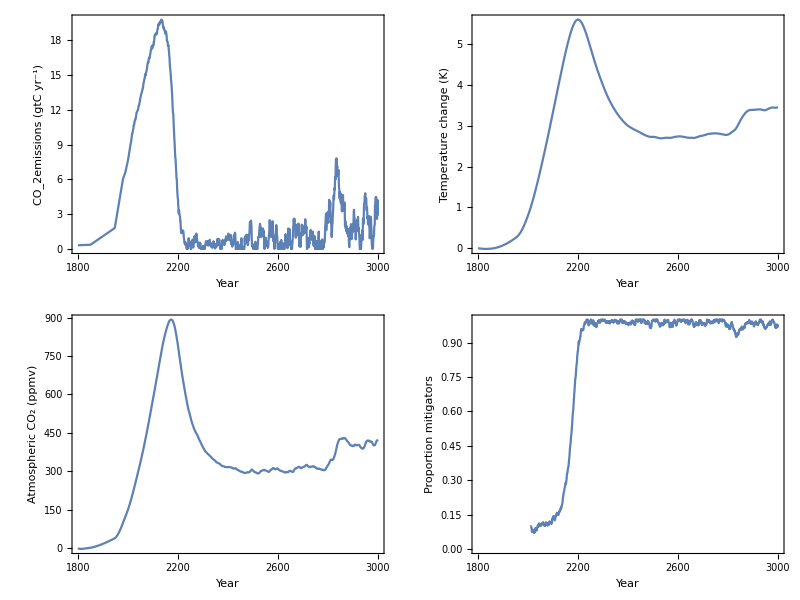

```mathematica
gridPlot=Grid[{{emissionPlot,tempPlot},{catPlot,socPlot}}]
```

## Export Data

```mathematica
seriesData={emissionSeries,y[[1]],y[[5]],y[[6]]};
```

```mathematica
Export["series_data/stoch_fun1_log.dat",seriesData];
```